## 1. GetVariance[ns, nph,Δprior] function

(*Function modified for Feedback*)

```mathematica
GetVariance[NumShots_,NumPhotons_,Δprior_]:=
Block[{(*all variables in this function are global*)},
(*We first calculate the probabilities for the first shot then change index of s to the shot number*)
(*This block outputs the matrix of probabilities for multiple photons and 2 shots, row represents shot number*)
Clear[γs1,φ,r,θ,Pmϕ,Δ,run];
Clear["θ*"];
Clear["r*"];
(*Set accuracy*)
accuracy = 5;
(*Uncertainty prior to this shot*)
Δ = Δprior;
(*number of shots*)
ns=NumShots;
(* Number of Photons *)
nph =NumPhotons;
(* Flat Prior P(ϕ)*)
Pϕ = 1/Δ;
(* creation Subscript[a, 1] out† and Subscript[a, 2 out]†*)
aDagger = {a1Dagger, a2Dagger};
(* annihilation*)
a = {a1,a2};
(*rk here represents Subscript[r, k],magnitude of input state coefficient*)
r=Table[Table[Symbol["r"<>ToString[k]<>"s"<>ToString[l]],{k,0,nph}],{l,1,ns}];
(*θk here represents Subscript[θ, k],real phase of input state coefficient(exponent)*)
θ=Table[Table[Symbol["θ"<>ToString[k]<>"s"<>ToString[l]],{k,0,nph}],{l,1,ns}];
(*Subscript[φ, k] here represents Subscript[ϕ̃, k] or the unbiased phase estimator*)
φ=Table[Table[Symbol["φm"<>ToString[l]<>"m"<>ToString[n]],{l,0,nph}],{n,0,nph}];
(*Pmxϕsy represent the conditional probability: mx-> x^th outcome, sy-> y^th shot*)
Pmϕ = Table[Table[Symbol["Pm"<>ToString[k]<>"ϕs"<>ToString[n]],{k,0,nph}],{n,1,ns}];
(*Final beamsplitter*)
MatrixForm[u2s1={{Cos[γs1], Sin[γs1]},{-Sin[γs1],Cos[γs1]}}];
ketΨp=∑_(n=0)^nph (r⟦1,n+1⟧ ⅇ^(ⅈ θ⟦1,n+1⟧) ⅇ^(ⅈ (nph-n) ϕ) x1^(nph-n) x2^n)/(√n! √(nph-n)!);
(*Matrix multiplication substitution*)
sub2={x1->u2s1⟦1,1⟧a1Dagger+u2s1⟦2,1⟧a2Dagger,x2->u2s1⟦1,2⟧a1Dagger+u2s1⟦2,2⟧a2Dagger};
(*a1dagger goes to a1*)
sub3=Table[aDagger⟦n⟧->a⟦n⟧,{n,1,2}];
(*Phase sign change due to complex conjugation*)
sub4={ϕ->-ϕ};
(*Phase sign change due to complex conjugation*)
sub5=Table[Table[θ⟦k,n⟧->-θ⟦k,n⟧,{n,1,nph+1}],{k,1,ns}];
(*the ket mentioned below is at |ψ'''>, after the final beamsplitter*)
ketΨppp=ketΨp/.sub2;
braΨppp=ketΨppp/.sub3/.sub4/.sub5;
γs1 = Pi/4;
(*multiply coefficients of braΨppp *)
bracket=Table[(nph-n)!*n!*Coefficient[braΨppp ketΨppp,a1Dagger^n a2Dagger^(nph-n)a1^n a2^(nph-n)],{n,0,nph}];
(*Assigning values from the bracket matrix to the Probability matrix*)
MatrixForm[Table[Pmϕ[[1,n]]=bracket[[n,1]],{n,1,nph+1}] ];
(*This should show probabilities for shot 1 only*)
(*MatrixForm[Pmϕ];*)
(*Rows of Pmϕ correspond to shots and columns correspond to different outcomes*)
(*Pmϕ[[shot#, outcome#]]*)
(*Changing s1 to ss for all values of Pmϕ[[1,k]] to Pmϕ[[s,k]]*)
Subs = Table[Table[{r[[1,k]]-> r[[s,k]],θ[[1,k]]-> θ[[s,k]]},{k,1,nph+1}],{s,2,ns}];
(*Implimenting the substitution*)
Table[Table[Pmϕ[[shot,n]] = Pmϕ[[1,n]]/.Flatten[Subs[[shot-1]]],{n,1,nph+1}],{shot,2,ns}];
(*Clears elements of listOfϕ and listOfPmϕ for another run*)
Clear["ϕm*"];
(*List of possible outcomes as a list of strings - m0, m1 and so on...*)
AllOutcomes = Table[ToString[Symbol["m"<>ToString[n]]],{n,0,nph}];
(*Declaring all phase estimators*)
(*Starts with the base case of ϕ*)
ϕ1st ={"ϕ"} ;
(*Appends all possible m# to ϕ as shots require*)
(*e.g if ns=3 then this creates ϕm0m0m0, ϕm0m0m1 and so on*)
Table[ϕ1st = Outer[StringJoin,ϕ1st,AllOutcomes],ns];
(*Flattening this weird list of lists*)
listOfϕ=Flatten[ϕ1st];
(*Making each element of this list a symbol of its own, not doing this results in issues later*)
listOfϕ = Table[Symbol[listOfϕ[[j]]],{j,1,(nph+1)^ns}];
(*Need a better method of clearing the values assigned to variables in a list*)
Clear["aϕ*"];
(*Generates a list of dummy phase estimators*)
listOfaϕ =Table[Symbol["a"<>ToString[listOfϕ[[n]]]],{n,1,(nph+1)^ns}];
(*Generate a list of a product of probabilities that matches the outcome sequence*)
(*e.g outcome sequence m0m2m1 has the corresponding product of probabilities attached Pm0ϕs1*Pm2ϕs2*Pm1ϕs3 *)
(*converting trig expression to exponential form is important otherwise some parts later don't run*)
listOfPmϕ =Flatten[Outer[Times,Sequence@@Pmϕ]];
(*change this line*)
(*Split expressions into ϕ-dependent and ϕ-indepedent terms*)
(*Collecting terms by changing variables*)
If[nph==1,expr=Table[Table[Coefficient[listOfPmϕ[[n]],Exp[ⅈ ϕ],k],{k,0,ns*nph}],{n,1,(nph+1)^ns}];,
zzz=Table[Collect[listOfPmϕ[[n]]/.ϕ->Log[q]/I,q],{n,1,(nph+1)^ns}];
(*selecting correct coefficients for the correct exponent*)
GetOrder=Table[Table[Exponent[zzz[[n,j]],q],{j,1,Length[zzz[[n]]]}],{n,1,(nph+1)^ns}];
(*Find the ordering that sorts the lists*)
SetOrder=Table[Ordering[GetOrder[[n]]],{n,1,(nph+1)^ns}];
(*Converting sums into a list,because operators disturb the implementation of the ordering*)
zzzlist=Table[Flatten[Table[List[zzz[[m,n]]],{n,1,Length[zzz[[m]]]}]],{m,1,(nph+1)^ns}];
(*Check*)
(*Table[Table[Exponent[zzzlist[[n,j]],q],{j,1,Length[zzzlist[[n]]]}],{n,1,(nph+1)^ns}]*)
(*Implementing the ordering*)
zzzrearranged=Table[Flatten[Table[List[zzzlist[[m,n]]],{n,1,Length[zzzlist[[m]]]}]][[SetOrder[[m]]]],{m,1,(nph+1)^ns}];
(* Check*)(*exponentsRearranged=Table[Table[Exponent[zzzrearranged[[n,j]],q],{j,1,Length[zzzrearranged[[n]]]}],{n,1,(nph+1)^ns}];*)

(*Select positive exponents only*)
zzzselect=Table[Table[If[Exponent[zzzrearranged[[n,j]],q]<0,zzzrearranged[[n,j]]=0,zzzrearranged[[n,j]]],{j,1,Length[zzzrearranged[[n]]]}],{n,1,(nph+1)^ns}];
(*Delete the elements which match 0 (terms with negative exponent )*)
zzzselect=Table[DeleteCases[zzzselect[[n]],0],{n,1,(nph+1)^ns}];
(*Look-up table for zzzselect*)
exponentsSelected=Table[Table[Exponent[zzzselect[[n,j]],q],{j,1,Length[zzzselect[[n]]]}],{n,1,(nph+1)^ns}];
expr=zzzselect;];
(*If nph is even then run the next section, *)
If[EvenQ[nph],
(*Continue running if nph is even: to account for the abnormality of the middle term*)
middleTerm=((nph+1)^ns+1)/2;
numberOf0s=Count[exponentsSelected[[middleTerm]],0];
(*Give middleTerm the same dimensionality of the previous array*)
expr[[middleTerm]]=expr[[middleTerm-1]];
(*Check/Look-up table*)
(*Table[Exponent[expr1[[middleTerm,j]],q],{j,1,Length[expr1[[middleTerm]]]}]*)

(*collect all constants and put them in the 1st cell*)
expr[[middleTerm,1]]=Sum[zzzselect[[middleTerm,j]],{j,1,numberOf0s}];
(*Check/Look-up table*)
(* Table[Exponent[expr[[middleTerm,j]],q],{j,1,Length[expr[[middleTerm]]]}]*)

(*collect all coefficients for even kth exponents and overwrite them in the 2k+1th cell*)
Table[expr[[middleTerm,2i+1]]=zzzselect[[middleTerm,numberOf0s+i]],{i,1,ns*nph/2}];
(*Check/Look-up table*)
(*Table[Exponent[expr[[middleTerm,j]],q],{j,1,Length[expr[[middleTerm]]]}]*)

(*all coefficients for odd exponents set to 0 and overwrite them in the 2kth cell*)
Table[expr[[middleTerm,2i]]=0,{i,1,ns*nph/2}];
(*Check/Look-up table*)
(*Table[Exponent[expr[[middleTerm,j]],q],{j,1,Length[expr[[middleTerm]]]}]*)

(*Drop terms after the last if there are - There might not be...need to check, since we took care of dimensionality earlier*)
expr[[middleTerm]]=Drop[expr[[middleTerm]],{ns*nph+2,Length[expr[[middleTerm]]]}];
(*Check/Look-up table*)
(*Table[Exponent[expr[[middleTerm,j]],q],{j,1,Length[expr[[middleTerm]]]}]*)
(*else leave the expression alone*)
,expr];
(*Check*)
exponentsSelected2=Table[Table[Exponent[expr[[n,j]],q],{j,1,Length[expr[[n]]]}],{n,1,(nph+1)^ns}];
(*Print[exponentsSelected2];*)

expr=expr/.q->1;
(*expr[[n,k+1]] n is outcome number and k+1 is the coefficient of e^ikϕ*)
(*Splitting constant terms from the others and adding complex conjugate terms to the other - This is a check, not to be fed into the integral-*)
(* exprSplit =Table[expr[[n,1]]+2*Sum[expr[[n,k+1]]*E^(ⅈ k ϕ),{k,1,ns*nph}],{n,1,(nph+1)^ns}];*)
(*This list contains all the phase estimators*)
(*Removed integration and substituted pre-calculated integrals*)
listOfϕ1=ParallelTable[Re[(2*Sum[expr[[n,k+1]]*-((ⅈ (k Δ Cos[(k Δ)/2]-2 Sin[(k Δ)/2]))/k^2),{k,1,ns*nph}])]/Re[(expr[[n,1]]*Δ+2*Sum[expr[[n,k+1]]*((2 Sin[(k Δ)/2])/k),{k,1,ns*nph}])],{n,1,(nph+1)^ns}];
(*ParallelTable or something causes listOfϕ to get the order reversed as per our conventions, reverting it back*)
(*We calculate the final variance using the dummy phase estimators*)
(*Removed integration and substituted pre-calculated integrals*)
(*This list contains all the variance values*)
listOfPartialVariance1 = ParallelTable[Pϕ*Re[expr[[n,1]]*(Δ^3/12)+2*Sum[expr[[n,k+1]]*((4 k Δ Cos[(k Δ)/2]+(-8+k^2 Δ^2) Sin[(k Δ)/2])/(2 k^3)),{k,1,ns*nph}] -4*listOfaϕ[[n]]*Sum[expr[[n,k+1]]*-((ⅈ (k Δ Cos[(k Δ)/2]-2 Sin[(k Δ)/2]))/k^2),{k,1,ns*nph}]+Δ*expr[[n,1]]*listOfaϕ[[n]]^2+2*listOfaϕ[[n]]^2*Sum[expr[[n,k+1]]*((2 Sin[(k Δ)/2])/k),{k,1,ns*nph}] ],{n,1,(nph+1)^ns}];
(*We calculated the final variance using the dummy phase estimators - listOfaϕ*)
(*And then replace the dummy phase estimators in 1.3.3 by the real ones calculated in 1.3.2*)
dummyFinalVariance1=Flatten[listOfPartialVariance1/.{Table[listOfaϕ[[n]]-> listOfϕ1[[n]],{n,1,(nph+1)^ns}]},1];

(*Normalizing the variance, each product normalizes 1 probability term in the product (of listOfPmϕ); e.g (1 /(r0s1^2+r1s1^2+r2s1^2)) normalizes Pm#ϕs1*)
normalizationTerm = ∏_(i=1)^ns 1/(∑_(s=1)^(nph+1) (r[[i,s]])^2);
(*Final variance*)
(*Sum is replaced by ParallelSum to decrease the time of computation*)
(*Note: We are ommitting Pϕ here since we have already taken that into consideration earlier while constructing dummyfinalvariance*)
finalVariance= normalizationTerm*Sum[dummyFinalVariance1[[j]], {j,1,(nph+1)^ns}];
(*While the imaginary term is essentially 0, mathematica may be calculating some expressions analytically and would keep ~0 imaginary values, therefore neglecting those*)
finalVariance = Re[finalVariance];
(* Print[finalVariance]; *)
Return[finalVariance]
(*Manual sanity check - Need to make it automatic*)
(*Print[Simplify[finalVariance/.{r0s1-> 1,r1s1-> 0,r2s1-> 0,r0s2-> 1,r1s2-> 0,r2s2-> 0},Assumptions-> Δ∈Reals]];*)]
```

## 2. ExtractOptState[delta,postVariance] Function

(*In case it takes too long change this version from 2.5 in that it simplifies optimization taking symmetry of states into account *)

```mathematica
ExtractOptState[delta_,PostVariance_]:=
(*Block or Module*)
Block[{Δ,OptimalrValues,variablelist,ListOfOptimalrValues,variablelistrandom,nrun,iteration,OptimalVariance,listforfindminimum,listOfLocalMinVariance,IndexMinVar,finalVariance},(*{"θ*","r*",(*list variables to keep local*)}*)
(*Generate a list to optimize over*)
Δ=delta;
finalVariance = PostVariance;
variablelist = Flatten[{θ,r}];
(*Generate a list of dummy optimization variable to assign a random starting point to them*)
variablelistrandom = ParallelTable[Symbol[ToString[variablelist[[l]]]<>"dummy"],{l,1,2*ns*(nph+1)}];
(*Give a random starting point to each dummy variable; θs are between -π and π while rs are between 0 and 1*)
(*run 50 iterations of findminimum*)
(*MaxIterations->∞;*)
nrun=20;
iteration=ParallelTable[
SeedRandom[];
Table[variablelistrandom[[n]] =RandomReal[{-π,π}],{n,1,ns*(nph+1)}];
Table[variablelistrandom[[n]] =RandomReal[{0,1}],{n,ns*(nph+1)+1,2*ns*(nph+1)}];
(*Arranging listforfindminimum to match FindMinimum syntax*)
listforfindminimum = Table[{variablelist[[n]],variablelistrandom[[n]]},{n,1,2*ns*(nph+1)}];
(*Print[listforfindminimum];*)
(*Optimization*)
(*Print[finalVariance];*)
FindMinimum[finalVariance,listforfindminimum,AccuracyGoal-> 5],{n,1,nrun}];
(*lower accuracy in case it takes too long*)
(*Print[iteration];*)
(*Finds the minimum from list of local minimums*)
listOfLocalMinVariance=Table[iteration[[n,1]],{n,1,nrun}];
IndexMinVar =Position[listOfLocalMinVariance,Min[listOfLocalMinVariance]]⟦1,1⟧;
OptimalVariance={iteration[[IndexMinVar,1]],Table[iteration[[IndexMinVar,2,n]],{n,1,Length[iteration[[IndexMinVar,2]]]}]};
(*Print[OptimalVariance];*)
(*Do we ignore the error we get in certain cases?*)
(*Extract minvalues for r variables*)
(*rcheck=Table[OptimalVariance[[2,n,1]],{n,ns*(nph+1)+1,Length[OptimalVariance[[2]]]}];*)
ListOfOptimalrValues=Table[OptimalVariance[[2,n,2]],{n,ns*(nph+1)+1,Length[OptimalVariance[[2]]]}];
(*Print[rcheck];*)
(*Partition lists into seperate shots*)
(*rchecksplit=Partition[rcheck,nph+1];*)
OptimalrValues=Partition[ListOfOptimalrValues,nph+1];
(*Normalizing over multiple shots*)
OptimalrValues = Table[Abs[Normalize[OptimalrValues[[n]]]],{n,1,ns}];
(*Print[OptimalrValues];*)
(*Return[OptimalrValues]*)
(*Print[rchecksplit];*)
(*plot[[plotnumber]]=Table[ListLinePlot[OptimalrValues[[n]],PlotLegends-> {OptimalVariance[[1]]},PlotLabel->Δ],{n,1,ns}]*)
Return[OptimalVariance];]
```

## 3. Scaling Formula by varying Nph, and Δ independently (independent of number of shots)

## Scaling formula for Gaussians and N00Ns

### Scaling formula by varying Δ

#### Nph=4

```mathematica
(*Run 1 shot calculations for different Δ*)
```

```mathematica
numPho=4;
InitialΔ=0.01;
DeltaΔ = InitialΔ;
Stepsize = 0.01;
```

```mathematica
GetUncertainties4=Table[
PostShot1Variance = GetVariance[1,numPho,DeltaΔ];
PostShot1State=ExtractOptState[DeltaΔ,PostShot1Variance];
(*Calculate uncertainty post shot*)
PostShot1Δ = √(12*PostShot1State[[1]]);
(*Generate new uncertainty*)
DeltaΔ=DeltaΔ+Stepsize;
(*Store that uncertainty*)
{PostShot1Δ},{i,1,Floor[π/Stepsize]}];
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::sdprec: Line search unable to find a sufficient decrease in the function value with MachinePrecision digit precision.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
FinalUncertainties4=Flatten[GetUncertainties4];
InitialUncertainties4 = Table[InitialΔ+n Stepsize,{n,0,Floor[π/Stepsize]-1}];
Data4=Thread[{InitialUncertainties4,FinalUncertainties4}];
(*Add element to DataN00N while Δ*Nph<5*)
DataN00N4={Data4[[1]]};
nstart=1;While[Data4[[nstart,1]]*numPho<10,Data4;nstart++];
DataG4=Table[Data4[[n]],{n,nstart,Length[Data4]}];
n=1;While[Data4[[n,1]]*numPho<2,AppendTo[DataN00N4,Data4[[n]]];n++];
(*If Δ(n+1)= Δ(n) + f'(Δ(n))*)
fprime4=Flatten[Table[Differences[DataN00N4[[n]]],{n,1,Length[DataN00N4]}]];
initialforfprime4=Table[n Stepsize,{n,1,Length[fprime4]}];
fprimefunction4=Thread[{initialforfprime4,fprime4}];
BestFitfprime4 = Fit[fprimefunction4,{1,x^3},x];
BestFitfprime4new = Fit[fprimefunction4,{1,x^4,x^3},x];
BestFit4N00N=Fit[DataN00N4,{1,x},x];
BestFit4G=Fit[DataG4,{1,√x},x];
```

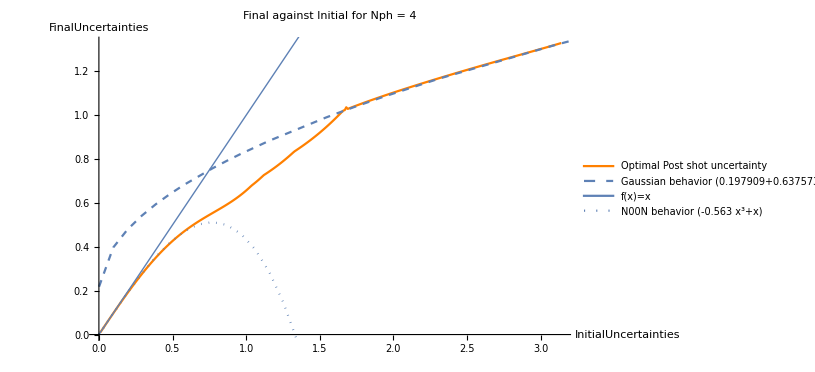

```mathematica
Show[ListLinePlot[Data4,PlotLabel-> "Final against Initial for Nph = 4",PlotStyle->Orange,PlotLegends->{"Optimal Post shot uncertainty"}],Plot[{BestFit4G},{x,0.001,Length[Data4]},PlotStyle-> Dashed, PlotLegends->{"Gaussian behavior"BestFit4G }],Plot[x,{x,0.001,Length[Data4]},PlotStyle->Thick,PlotLegends-> {"f(x)=x"}],Plot[x-0.563x^3,{x,0.001,Length[Data4]},PlotStyle->Dotted,PlotLegends-> {"N00N behavior (-0.563 x^3+x)"}],AxesLabel-> {"InitialUncertainties","FinalUncertainties"}]
```

```mathematica
(*For Gaussian regime, Subscript[Δ, f]∝(√Subscript[Δ, i])/(√N). Subscript[Δ, f]=const(√Subscript[Δ, i])/(√N). Subscript[Δ, f]≃0.6375730913649863 √Subscript[Δ, i], for N=4. Therefore const = 2*0.6375730913649863=1.2751461827299726*)
```

```mathematica
(*Plot final - initial uncertainty*)
```

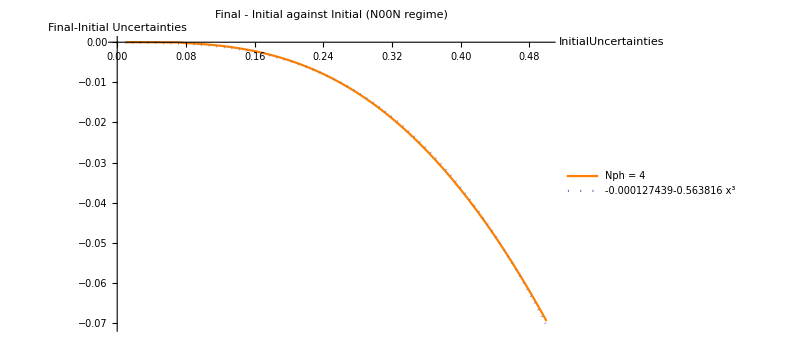

```mathematica
Show[ListLinePlot[fprimefunction4,PlotLabel-> "Final - Initial against Initial (N00N regime)",PlotStyle->Orange,PlotLegends->{"Nph = 4"}],Plot[BestFitfprime4,{x,0,Length[fprimefunction4]/100},PlotStyle-> Dotted, PlotLegends->{BestFitfprime4}],AxesLabel-> {"InitialUncertainties","Final-Initial Uncertainties"},PlotRange-> Automatic]
```

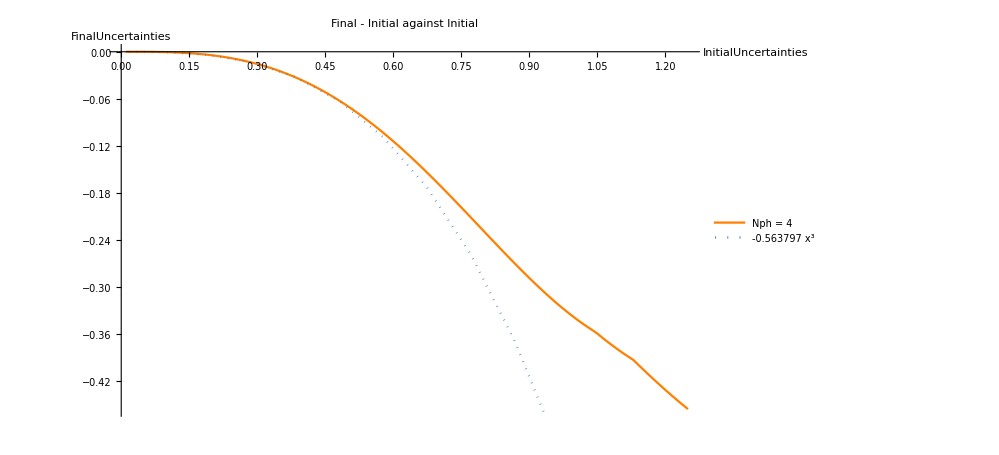

```mathematica
Show[ListLinePlot[fprimefunction4,PlotLabel-> "Final - Initial against Initial",PlotStyle->Orange,PlotLegends->{"Nph = 4"}],Plot[{-0.5637973439290543 x^3},{x,0,Length[Data4]},PlotStyle-> Dotted, PlotLegends->{-0.5637973439290543 x^3}],AxesLabel-> {"InitialUncertainties","Final-Initial Uncertainty"}]
```

```mathematica
(*For N00N, dΔ = - Subscript[c, 1]*Nph*y^2 ⇒ 1/Subscript[Δ, req]-1/Subscript[Δ, i] = Subscript[c, 1]*Nph*Ns + Subscript[c, 2]. Subscript[c, 1]=0.321044854697679/Nph = 0.08*)
```

```mathematica
0.3210448055997048/4
```

0.0802612

#### Nph=9

```mathematica
(*Run 1 shot calculations for different Δ*)
```

```mathematica
numPho=9;
InitialΔ=0.01;
DeltaΔ = InitialΔ;
Stepsize = 0.01;
```

```mathematica
GetUncertainties9=Table[
PostShot1Variance = GetVariance[1,numPho,DeltaΔ];
PostShot1State=ExtractOptState[DeltaΔ,PostShot1Variance];
(*Calculate uncertainty post shot*)
PostShot1Δ = √(12*PostShot1State[[1]]);
(*Generate new uncertainty*)
DeltaΔ=DeltaΔ+Stepsize;
(*Store that uncertainty*)
{PostShot1Δ},{i,1,Floor[π/Stepsize]}];
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::sdprec: Line search unable to find a sufficient decrease in the function value with MachinePrecision digit precision.

```mathematica
FinalUncertainties9=Flatten[GetUncertainties9];
InitialUncertainties9 = Table[InitialΔ+n Stepsize,{n,0,Floor[π/Stepsize]-1}];
Data9=Thread[{InitialUncertainties9,FinalUncertainties9}];
(*Add element to DataN00N while Δ*Nph<5*)
DataN00N9={Data9[[1]]};
nstart=1;While[Data9[[nstart,1]]*numPho<10,Data9;nstart++];
DataG9=Table[Data9[[n]],{n,nstart,Length[Data9]}];
n=1;While[Data9[[n,1]]*numPho<2,AppendTo[DataN00N9,Data9[[n]]];n++];
(*If Δ(n+1)= Δ(n) + f'(Δ(n))*)
fprime9=Flatten[Table[Differences[DataN00N9[[n]]],{n,1,Length[DataN00N9]}]];
initialforfprime9=Table[n Stepsize,{n,1,Length[fprime9]}];
fprimefunction9=Thread[{initialforfprime9,fprime9}];
BestFitfprime9 = Fit[fprimefunction9,{1,x^3},x];
BestFit9N00N=Fit[DataN00N9,{1,x},x];
BestFit9G=Fit[DataG9,{1,√x},x];
```

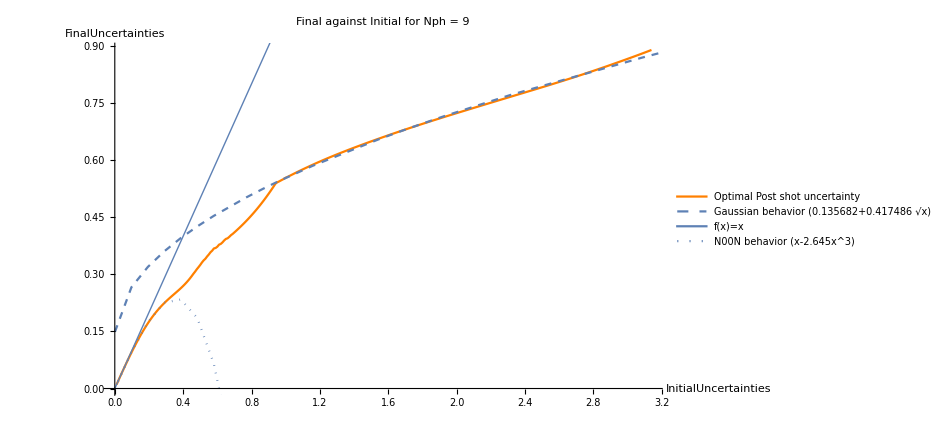

```mathematica
Show[ListLinePlot[Data9,PlotLabel-> "Final against Initial for Nph = 9",PlotStyle->Orange,PlotLegends->{"Optimal Post shot uncertainty"}],Plot[{BestFit9G},{x,0.001,Length[Data9]},PlotStyle-> Dashed, PlotLegends->{"Gaussian behavior"BestFit9G }],Plot[x,{x,0.001,Length[Data9]},PlotStyle->Thick,PlotLegends-> {"f(x)=x"}],Plot[x-2.645x^3,{x,0.001,Length[Data9]},PlotStyle->Dotted,PlotLegends-> {"N00N behavior (x-2.645x^3)"}],AxesLabel-> {"InitialUncertainties","FinalUncertainties"}]
```

```mathematica
(*For Gaussian regime, Subscript[Δ, f]∝(√Subscript[Δ, i])/(√N). Subscript[Δ, f]=const(√Subscript[Δ, i])/(√N). Subscript[Δ, f]≃0.4174863543439747 √Subscript[Δ, i], for N=9. Therefore const = 3*0.4174863543439747=1.2524590630319241*)
```

```mathematica
(*Plot final - initial uncertainty*)
```

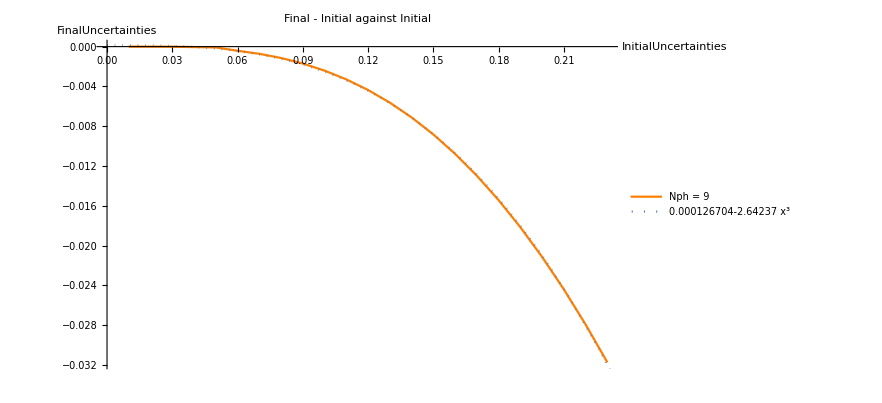

```mathematica
Show[ListLinePlot[fprimefunction9,PlotLabel-> "Final - Initial against Initial",PlotStyle->Orange,PlotLegends->{"Nph = 9"}],Plot[{BestFitfprime9},{x,0,Length[fprimefunction9]},PlotStyle-> Dotted, PlotLegends->{BestFitfprime9}],AxesLabel-> {"InitialUncertainties","FinalUncertainties"}]
```

```mathematica
(*For N00N, dΔ = - Subscript[c, 1]*Nph*y^2 ⇒ 1/Subscript[Δ, req]^2-1/Subscript[Δ, i]^2 = Subscript[c, 1]*Nph^2*Ns + Subscript[c, 2]. Subscript[c, 1]=0.7021216145141785/Nph = 0.078*)
```

```mathematica
0.7021216145141785/9
```

0.0780135

#### Nph=13

```mathematica
(*Run 1 shot calculations for different Δ*)
```

```mathematica
numPho=13;
InitialΔ=0.01;
DeltaΔ = InitialΔ;
Stepsize = 0.01;
```

```mathematica
GetUncertainties13=Table[
PostShot1Variance = GetVariance[1,numPho,DeltaΔ];
PostShot1State=ExtractOptState[DeltaΔ,PostShot1Variance];
(*Calculate uncertainty post shot*)
PostShot1Δ = √(12*PostShot1State[[1]]);
(*Generate new uncertainty*)
DeltaΔ=DeltaΔ+Stepsize;
(*Store that uncertainty*)
{PostShot1Δ},{i,1,Floor[π/Stepsize]}];
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

```mathematica
FinalUncertainties13=Flatten[GetUncertainties13];
InitialUncertainties13 = Table[InitialΔ+n Stepsize,{n,0,Floor[π/Stepsize]-1}];
Data13=Thread[{InitialUncertainties13,FinalUncertainties13}];
(*Add element to DataN00N while Δ*Nph<5*)
DataN00N13={Data13[[1]]};
nstart=1;While[Data13[[nstart,1]]*numPho<10,Data13;nstart++];
DataG13=Table[Data13[[n]],{n,nstart,Length[Data13]}];
n=1;While[Data13[[n,1]]*numPho<2,AppendTo[DataN00N13,Data13[[n]]];n++];
(*If Δ(n+1)= Δ(n) + f'(Δ(n))*)
fprime13=Flatten[Table[Differences[DataN00N13[[n]]],{n,1,Length[DataN00N13]}]];
initialforfprime13=Table[n Stepsize,{n,1,Length[fprime13]}];
fprimefunction13=Thread[{initialforfprime13,fprime13}];
BestFitfprime13 = Fit[fprimefunction13,{1,x^3},x];
BestFit13N00N=Fit[DataN00N13,{1,x},x];
BestFit13G=Fit[DataG13,{1,√x},x];
```

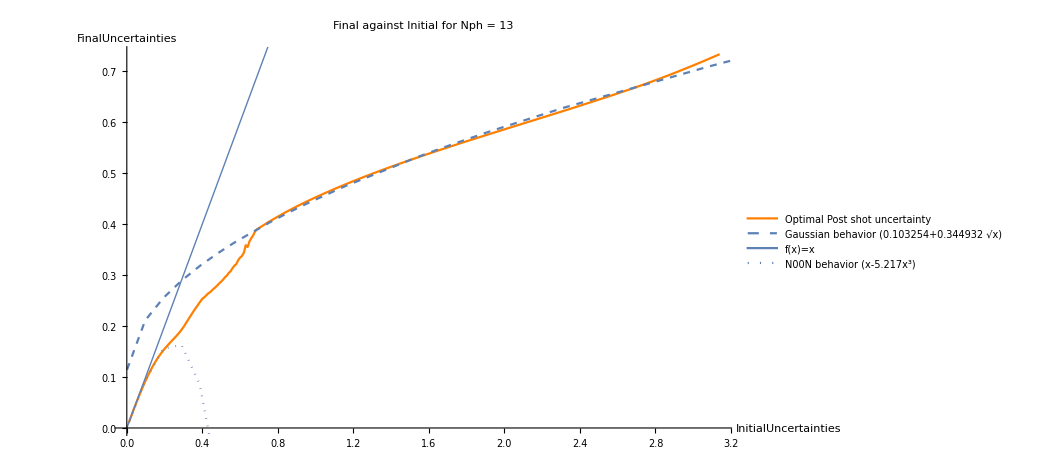

```mathematica
Show[ListLinePlot[Data13,PlotLabel-> "Final against Initial for Nph = 13",PlotStyle->Orange,PlotLegends->{"Optimal Post shot uncertainty"}],Plot[{BestFit13G},{x,0.001,Length[Data13]},PlotStyle-> Dashed, PlotLegends->{"Gaussian behavior"BestFit13G }],Plot[x,{x,0.001,Length[Data13]},PlotStyle->Thick,PlotLegends-> {"f(x)=x"}],Plot[x-5.217x^3,{x,0.001,Length[Data13]},PlotStyle->Dotted,PlotLegends-> {"N00N behavior (x-5.217x^3)"}],AxesLabel-> {"InitialUncertainties","FinalUncertainties"}]
```

```mathematica
(*For Gaussian regime, Subscript[Δ, f]∝(√Subscript[Δ, i])/(√N). Subscript[Δ, f]=const(√Subscript[Δ, i])/(√N). Subscript[Δ, f]≃0.3449319668851363 √Subscript[Δ, i], for N=9. Therefore const = √13*0.3449319668851363=1.2436698931510055*)
```

```mathematica
(*Plot final - initial uncertainty*)
```

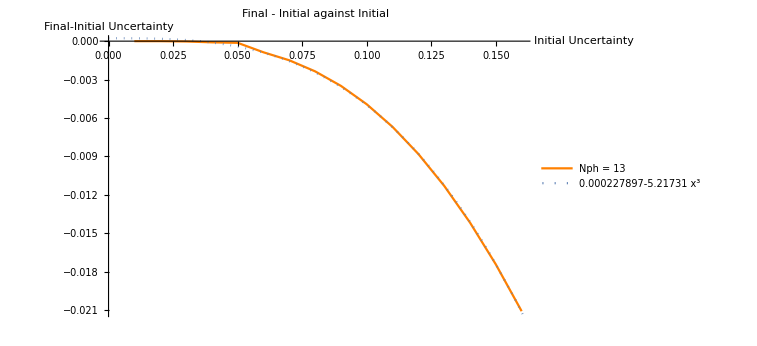

```mathematica
Show[ListLinePlot[fprimefunction13,PlotLabel-> "Final - Initial against Initial",PlotStyle->Orange,PlotLegends->{"Nph = 13"}],Plot[{BestFitfprime13},{x,0,Length[fprimefunction13]},PlotStyle-> Dotted, PlotLegends->{BestFitfprime13}],AxesLabel-> {"Initial Uncertainty","Final-Initial Uncertainty"}]
```

```mathematica
(*scale with Nph*)
```

```mathematica
(*For N00N, dΔ = - Subscript[c, 1]*Nph*Δ^2 ⇒ 1/Subscript[Δ, req]^2-1/Subscript[Δ, i]^2 = Subscript[c, 1]*Nph^2*Ns + Subscript[c, 2]. Subscript[c, 1]=0.9980003056361779/Nph = 0.077*)
```

```mathematica
0.9980003056361779/13
```

0.0767693

### Scaling formula by varying Nph

```mathematica
(*Coefficient dependence with Nph*)
```

#### Δ = π (for Gaussian)

```mathematica
Clear[numPho];
InitialDelta = π;
Nph=20;
```

```mathematica
GetUncertaintiesπ=Table[
PostShot1Variance = GetVariance[1,numPho,InitialDelta];
PostShot1State=ExtractOptState[InitialDelta,PostShot1Variance];
(*Calculate uncertainty post shot*)
PostShot1Δ = √(12*PostShot1State[[1]]);
{PostShot1Δ},{numPho,1,Nph}];
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

```mathematica
(*Plot Final uncertainty vs Nph*)
```

```mathematica
GetUncertaintiesπ = Flatten[GetUncertaintiesπ]
```

{2.23745,1.78722,1.51426,1.32961,1.19544,1.0929,1.01152,0.944997,0.889362,0.84196,0.80096,0.765054,0.733277,0.704902,0.679367,0.656235,0.635154,0.615841,0.598065,0.581635}

```mathematica
BestFitπ = Fit[GetUncertaintiesπ,{1,1/(√x)},x]
```

0.123049+2.25855/(√x)

```mathematica
(*Looking for 1/√Nph behavior*)
```

```mathematica
πfunc = Table[π,{n,1,Nph}]
```

{π,π,π,π,π,π,π,π,π,π,π,π,π,π,π,π,π,π,π,π}

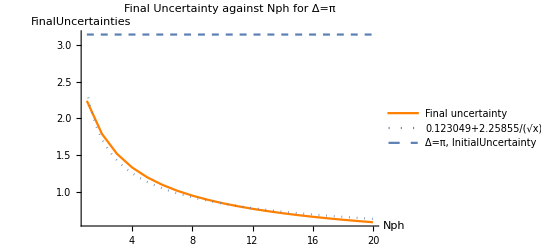

```mathematica
Show[ListLinePlot[GetUncertaintiesπ,PlotStyle->Orange,PlotLegends->{"Final uncertainty"}],Plot[{BestFitπ},{x,0,Nph},PlotStyle-> Dotted, PlotLegends->{BestFitπ}],ListLinePlot[πfunc,PlotStyle->Dashed,PlotLegends-> {"Δ=π, InitialUncertainty"}],AxesLabel-> {"Nph","FinalUncertainties"},PlotLabel-> "Final Uncertainty against Nph for Δ=π",PlotRange->All]
```

```mathematica
(*Find constant of proportionality*)
```

```mathematica
2.258545685940095/(√π)
```

1.27425

#### Δ = π/20 (for N00N)

```mathematica
Clear[numPho];
InitialDelta = π/20;
Nph=20;
```

```mathematica
GetUncertaintiesπb10=Table[
PostShot1Variance = GetVariance[1,numPho,InitialDelta];
PostShot1State=ExtractOptState[InitialDelta,PostShot1Variance];
(*Calculate uncertainty post shot*)
PostShot1Δ = √(12*PostShot1State[[1]]);
{PostShot1Δ},{numPho,1,Nph}];
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
(*Plot Final uncertainty vs Nph*)
```

```mathematica
GetUncertaintiesπb10 = Flatten[GetUncertaintiesπb10]
```

{0.156918,0.156436,0.155636,0.154526,0.153115,0.151417,0.149447,0.147224,0.144769,0.142107,0.139266,0.136278,0.133176,0.129999,0.126788,0.123588,0.120446,0.117411,0.114536,0.111873}

```mathematica
BestFitπb10 = Fit[GetUncertaintiesπb10,{1,x^3},x]
```

0.0499781-3.07325×10^-7 x^3

```mathematica
(*Looking for Nph dependence for N00Ns*)
```

```mathematica
πb10func = Table[1/20,{n,1,Nph}]
```

{1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20}

```mathematica
(*If Δ(n+1)= Δ(n) + f'(Δ(n))*)
```

```mathematica
ΔDiff = 1/GetUncertaintiesπb10^2-1/InitialDelta^2
```

{0.0834019,0.334429,0.755539,1.35081,2.12587,3.08788,4.24532,5.60783,7.18586,8.99016,11.031,13.3172,15.8545,18.6439,21.6788,24.9423,28.4031,32.0123,35.7,39.3726}

```mathematica
ΔDiff2 = Take[ΔDiff,10]
```

{359.555,359.715,360.106,360.21,360.734,361.696,360.819,362.418,366.267,362.008}

```mathematica
ΔDiffnew = (GetUncertaintiesπb10-InitialDelta)/InitialDelta^3
```

{-0.0416367,-0.166187,-0.372568,-0.658975,-1.02287,-1.46097,-1.96924,-2.54288,-3.1763,-3.8631,-4.59608,-5.36716,-6.16743,-6.9871,-7.81553,-8.64125,-9.45202,-10.235,-10.9768,-11.664}

```mathematica
DiffBestFitnew = Fit[ΔDiffnew,{1,x^2},x]
```

-0.0347237-0.0387727 x^2

```mathematica
DiffBestFit = Fit[ΔDiff,{1,x^2},x]
```

-0.523159+0.099368 x^2

```mathematica
(*Plot 1/final - 1/initial uncertainty*)
```

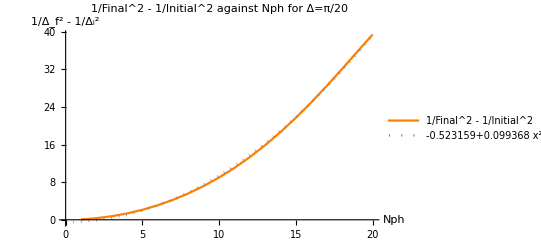

```mathematica
Show[ListLinePlot[ΔDiff,PlotStyle->Orange,PlotLegends->{"1/Final^2 - 1/Initial^2"}],Plot[DiffBestFit,{x,0,Nph},PlotStyle-> Dotted, PlotLegends->{DiffBestFit}],AxesLabel-> {"Nph","1/Δ_f^2 - 1/Δ_i^2"},PlotLabel-> "1/Final^2 - 1/Initial^2 against Nph for Δ=π/20",PlotRange->All]
```

```mathematica
(*1/Δreq^2 - 1/Δi^2 = Subscript[c, 1]*Nph^2*Ns. Subscript[c, 1]=0.1 *)
```

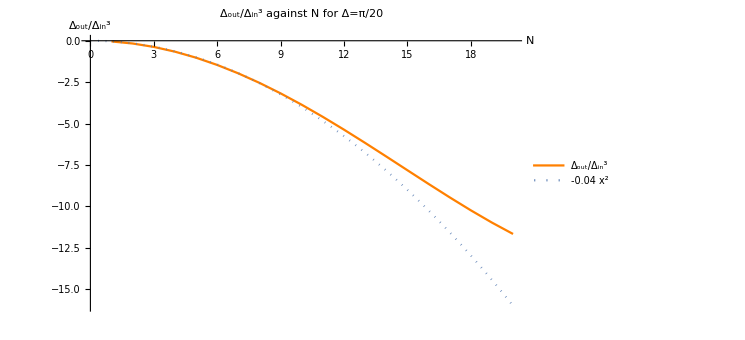

```mathematica
Show[ListLinePlot[ΔDiffnew,PlotStyle->Orange,PlotLegends->{"Δ_out/Δ_in^3"}],Plot[-0.04x^2,{x,0,Nph},PlotStyle-> Dotted, PlotLegends->{-0.04x^2}],AxesLabel-> {"N","Δ_out/Δ_in^3"},PlotLabel-> "Δ_out/Δ_in^3 against N for Δ=π/20",PlotRange->All]
```

## Predicted scaling formulas

### Gaussian Scaling: We show that Δ_f=const(√Δ_i)/(√Nph), where const ≃1.27

#### By plotting Δ_f(Δ_i), keeping Nph constant

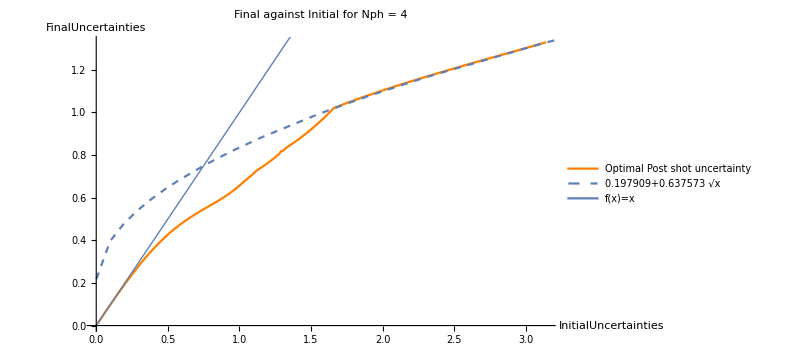

```mathematica
(*Optimal post shot uncertainty as a function of initial input uncertainty for Nph=4*)
```

```mathematica
(*For Gaussian regime, Subscript[Δ, f]∝(√Subscript[Δ, i])/(√N). Subscript[Δ, f]=const(√Subscript[Δ, i])/(√N). Subscript[Δ, f]≃0.6375730913649863 √Subscript[Δ, i], for Nph=4. Therefore const = 2*0.6375730913649863=1.2751461827299726*)
```

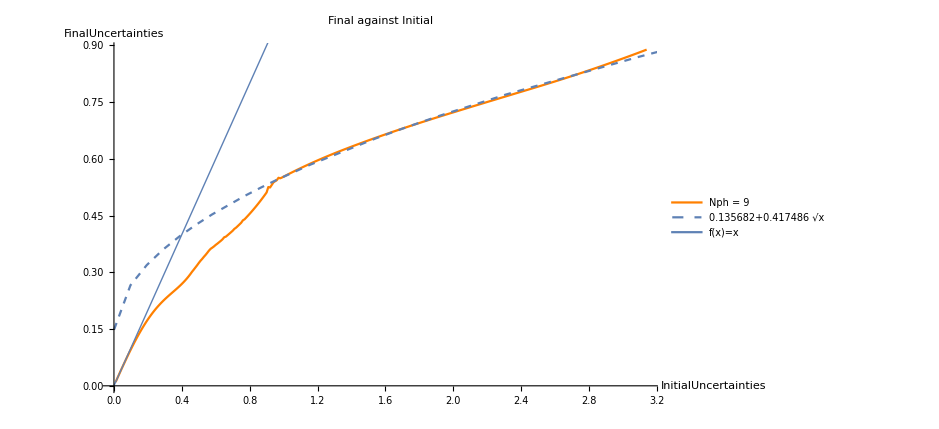

```mathematica
(*Optimal post shot uncertainty as a function of initial input uncertainty for Nph=9*)
```

```mathematica
(*For Gaussian regime, Subscript[Δ, f]∝(√Subscript[Δ, i])/(√N). Subscript[Δ, f]=const(√Subscript[Δ, i])/(√N). Subscript[Δ, f]≃0.4174863543439747 √Subscript[Δ, i], for N=9. Therefore const = 3*0.4174863543439747=1.2524590630319241*)
```

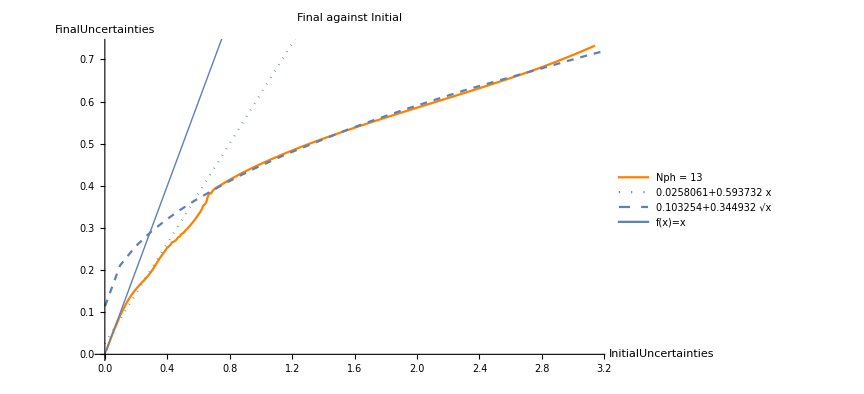

```mathematica
(*Optimal post shot uncertainty as a function of initial input uncertainty for Nph=13*)
```

```mathematica
(*For Gaussian regime, Subscript[Δ, f]∝(√Subscript[Δ, i])/(√N). Subscript[Δ, f]=const(√Subscript[Δ, i])/(√N). Subscript[Δ, f]≃0.3449319668851363 √Subscript[Δ, i], for N=9. Therefore const = √13*0.3449319668851363=1.2436698931510055*)
```

#### By plotting Δ_f(Nph), keeping Δ_i constant

```mathematica
(*Optimal post shot uncertainty as a function of Nph for Δ=π(which is in the Gaussian regime for all Nph>1)*)
```

-Graphics-

```mathematica
(*For Gaussian regime, Subscript[Δ, f]∝(√Subscript[Δ, i])/(√N). Subscript[Δ, f]=const(√Subscript[Δ, i])/(√N). Subscript[Δ, f]≃2.258545685940095/(√N), for Δ=π. Therefore const = 2.258545685940095/(√π)=1.274247949974124*)
```

```mathematica
(*Find constant of proportionality*)
```

```mathematica
2.258545685940095/(√π)
```

1.27425

### N00N Scaling: We show that Δ = - c_1*Nph^2*Δ^3 Ns ⇒1/Δ_req^2-1/Δ_i^2 =2 c_1 Nph^2 Ns + c_2(Nph), where c1 ≃0.04, c_2 should match the following boundary condition: For Δ_req=Δ_i, LHS = 0, Ns=0 ⇒ c_2=0.

#### By plotting (Δ_req-Δ_i)(Δ_i), keeping Nph constant, we show that c_1≃0.03

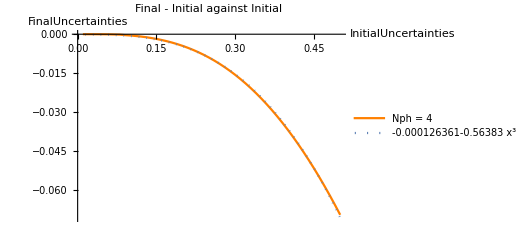

```mathematica
(*For Nph=4*)
```

```mathematica
(*For N00N regime, for dNs=1 (only 1 shot increment), dΔ = - Subscript[c, 1]*Nph^2*Δ^3 ⇒  Subscript[c, 1]=0.563829997419515/Nph^2 = 0.03523937483871969*)
```

```mathematica
0.563829997419515/16
```

0.0352394

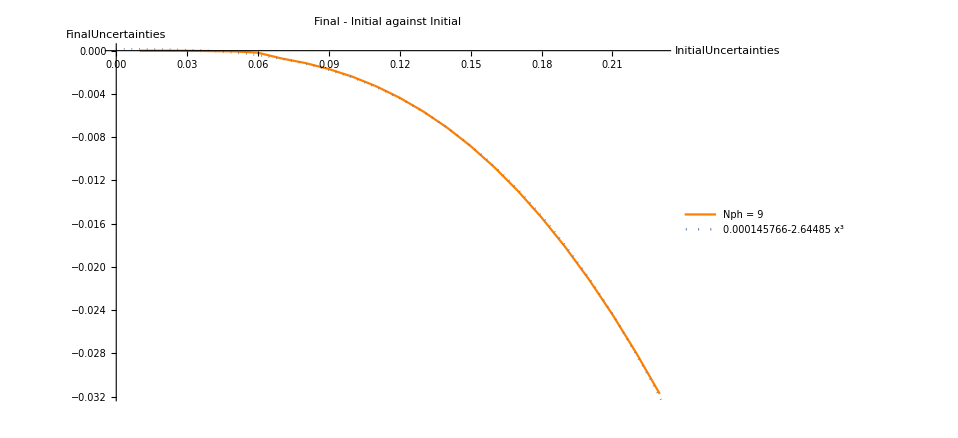

```mathematica
(*For Nph=9*)
```

```mathematica
(*For N00N, for dNs=1 (only 1 shot increment), dΔ = - Subscript[c, 1]*Nph*Δ^3. Subscript[c, 1]=2.6448512886615014/Nph^2 = 0.03265248504520372*)
```

```mathematica
2.6448512886615014/81
```

0.0326525

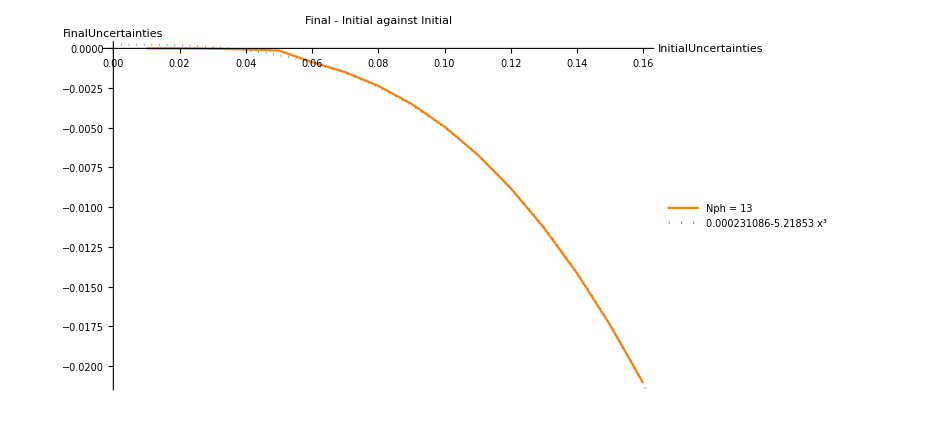

```mathematica
(*For Nph=13*)
```

```mathematica
(*For N00N, for dNs=1 (only 1 shot increment), dΔ = - Subscript[c, 1]*Nph^2*Δ^2. Subscript[c, 1]=5.218526565472027/Nph^2 = 0.03087885541699424*)
```

#### By plotting (1/Δ_req^2-1/Δ_i^2)(Nph), keeping Δ_i constant, we show that 2 c_1≃0.1 ⇒c_1≃0.05

0.0308789

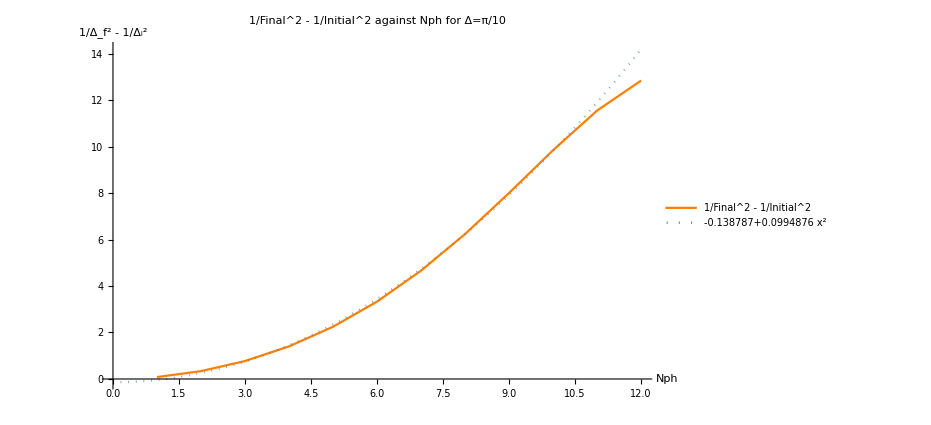

```mathematica
5.218526565472027/169
```

```mathematica
(*1/Δreq^2 - 1/Δi^2 = Subscript[c, 1]*Nph^2*Ns. Subscript[c, 1]=0.1 *)
```

#### By plotting ((Δ_req-Δ_i)/Δ_i^3)(Nph), keeping Δ_i constant, we show that c_1≃0.1 ⇒c_1≃0.04

0.0308789

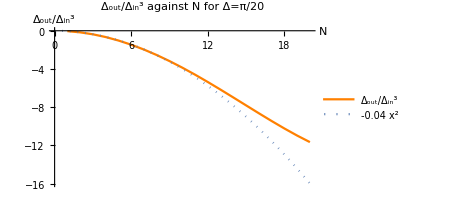

```mathematica
5.218526565472027/169
```

```mathematica
(* ((Subscript[Δ, req]-Subscript[Δ, i])/Subscript[Δ, i]^3) = - Subscript[c, 1]*Nph^2. Subscript[c, 1]= 0.04*)
```

## Predicted scaling formula compared with optimal iterated scaling

### Optimal iterative scaling

#### Function

```mathematica
(*Start with a given uncertainty*)
```

```mathematica
(*Given StartingΔ, returns PostShot1Δ after 1 shot*)
```

```mathematica
Iterate[StartingΔ_]:=Block[{PostShot1Variance,PostShot1State},
PostShot1Variance = GetVariance[1,numPho,StartingΔ];
PostShot1State=ExtractOptState[StartingΔ,PostShot1Variance];
(*Calculate uncertainty post shot*)
PostShot1Δ = √(12*PostShot1State[[1]]);
(*Print[PostShot1Δ];*)];
```

#### Strictly Gaussian

```mathematica
(*Strictly gaussian*)
```

```mathematica
numPho=9;
StartingΔ=π;
RequiredΔ = 0.5;
```

```mathematica
Δ1=StartingΔ;
(*Print[N[Δ1]];*)
ΔList = {Δ1};
Steps = 0;
While[Δ1>RequiredΔ,Iterate[Δ1];Δ1=PostShot1Δ;AppendTo[ΔList,Δ1];Steps++ ];
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

```mathematica
Print[ΔList];
Print["Number of shot = ",Steps];
```

{π,0.889362,0.504756,0.326817}

Number of shot = 3

#### Strictly N00N

```mathematica
(*Strictly N00N*)
```

```mathematica
numPho=9;
StartingΔ=π/15;
RequiredΔ = π/20;
```

```mathematica
Δ1=StartingΔ;
(*Print[N[Δ1]];*)
ΔList = {Δ1};
Steps = 0;
While[Δ1>RequiredΔ,Iterate[Δ1];Δ1=PostShot1Δ;AppendTo[ΔList,Δ1];Steps++ ];
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

```mathematica
Print[ΔList];
Print["Number of shot = ",Steps];
```

{π/15,0.181704,0.163057,0.149354}

Number of shot = 3

#### Mixed

```mathematica
(*Mixed*)
```

```mathematica
numPho=9;
StartingΔ=π;
RequiredΔ = π/20;
```

```mathematica
Δ1=StartingΔ;
(*Print[N[Δ1]];*)
ΔList = {Δ1};
Steps = 0;
While[Δ1>RequiredΔ,Iterate[Δ1];Δ1=PostShot1Δ;AppendTo[ΔList,Δ1];Steps++ ];
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
Print[ΔList];
Print["Number of shot = ",Steps];
```

{π,0.889362,0.504756,0.327043,0.239995,0.199837,0.175485,0.15859,0.145936}

Number of shot = 8

#### Mixed trial 2

```mathematica
(*Mixed*)
```

```mathematica
numPho=13;
StartingΔ=π;
RequiredΔ = 0.05;
```

```mathematica
Δ1=StartingΔ;
(*Print[N[Δ1]];*)
ΔList = {Δ1};
Steps = 0;
While[Δ1>RequiredΔ,Iterate[Δ1];Δ1=PostShot1Δ;AppendTo[ΔList,Δ1];Steps++ ];
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

```mathematica
Print[ΔList];
Print["Number of shot = ",Steps];
```

{π,0.733277,0.399778,0.252949,0.176527,0.143896,0.125094,0.112387,0.10302,0.0957273,0.0898314,0.0849313,0.0807716,0.0771809,0.074039,0.0712586,0.0687747,0.0665377,0.0645088,0.0626574,0.0609588,0.059393,0.0579435,0.0565963,0.05534,0.0541646,0.0530618,0.0520245,0.0510462,0.0501216,0.049246}

Number of shot = 30

#### Mixed trial 3

```mathematica
(*Mixed*)
```

```mathematica
numPho=9;
StartingΔ=π;
RequiredΔ = 0.05;
```

```mathematica
Δ1=StartingΔ;
(*Print[N[Δ1]];*)
ΔList = {Δ1};
Steps = 0;
While[Δ1>RequiredΔ,Iterate[Δ1];Δ1=PostShot1Δ;AppendTo[ΔList,Δ1];Steps++ ];
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
Print[ΔList];
Print["Number of shot = ",Steps];
```

{π,0.889362,0.518256,0.335357,0.243266,0.201634,0.176668,0.159448,0.146596,0.136508,0.128304,0.121455,0.11562,0.110569,0.106139,0.102212,0.098697,0.0955272,0.0926488,0.0900194,0.0876047,0.0853768,0.0833128,0.0813932,0.0796019,0.0779251,0.076351,0.0748696,0.073472,0.0721505,0.0708985,0.0697101,0.0685799,0.0675034,0.0664765,0.0654954,0.0645568,0.0636578,0.0627955,0.0619676,0.0611718,0.0604061,0.0596686,0.0589576,0.0582717,0.0576092,0.056969,0.0563498,0.0557504,0.0551699,0.0546073,0.0540616,0.053532,0.0530178,0.0525181,0.0520325,0.0515612,0.0513264,0.0508928,0.0506112,0.0501763,0.0500014,0.049582}

Number of shot = 62

### Predicted iterative scaling

#### Functions

```mathematica
UseN00NScaling[InitialΔ_]:=Block[{(*After 1 shot*)},Print["N"];Subscript[Δ, f]= InitialΔ/(√(1+2*0.04*InitialΔ^2* numPho^2)) ; Return[Subscript[Δ, f]]];
```

```mathematica
UseGaussianScaling[InitialΔ_]:=Block[{(*After 1 shot*)},Print["G"];Subscript[Δ, f]=1.27 (√InitialΔ)/(√numPho) ; Return[Subscript[Δ, f]]];
```

```mathematica
PredictIterate[StartingΔ_]:=Block[{PostShot1Variance,PostShot1State},
If[StartingΔ*numPho>2,PostShot1Δ =UseGaussianScaling[StartingΔ],PostShot1Δ = UseN00NScaling[StartingΔ]]
(*Calculate uncertainty post shot*)
(*Print[PostShot1Δ];*)];
```

#### Strictly Gaussian

```mathematica
numPho=9;
StartingΔ=π;
RequiredΔ = 0.5;
```

```mathematica
Δ2=StartingΔ;
(*Print[N[Δ1]];*)
ΔList2 = {Δ2};
Steps2 = 0;
While[Δ2>RequiredΔ,PredictIterate[Δ2];Δ2=PostShot1Δ;AppendTo[ΔList2,Δ2];Steps2++ ];
```

G

G

```mathematica
Print[ΔList2];
Print["Number of shot = ",Steps2];
```

{π,0.750339,0.3667}

Number of shot = 2

#### Strictly N00N

```mathematica
numPho=9;
StartingΔ=π/15;
RequiredΔ = π/20;
```

```mathematica
Δ2=StartingΔ;
(*Print[N[Δ1]];*)
ΔList2 = {Δ2};
Steps2 = 0;
While[Δ2>RequiredΔ,PredictIterate[Δ2];Δ2=PostShot1Δ;AppendTo[ΔList2,Δ2];Steps2++ ];
```

N

N

N

```mathematica
Print[ΔList2];
Print["Number of shot = ",Steps2];
```

{π/15,0.184814,0.167231,0.153869}

Number of shot = 3

#### Mixed

```mathematica
numPho=9;
StartingΔ=π;
RequiredΔ = π/20;
```

```mathematica
Δ2=StartingΔ;
(*Print[N[Δ1]];*)
ΔList2 = {Δ2};
Steps2 = 0;
While[Δ2>RequiredΔ,PredictIterate[Δ2];Δ2=PostShot1Δ;AppendTo[ΔList2,Δ2];Steps2++ ];
```

G

G

G

«1 more identical outputs»

N

N

N

```mathematica
Print[ΔList2];
Print["Number of shot = ",Steps2];
```

{π,0.750339,0.3667,0.256353,0.214339,0.188154,0.169694,0.155781}

Number of shot = 7

#### Mixed trial 2

```mathematica
numPho=13;
StartingΔ=π;
RequiredΔ = 0.05;
```

```mathematica
Δ2=StartingΔ;
(*Print[N[Δ1]];*)
ΔList2 = {Δ2};
Steps2 = 0;
While[Δ2>RequiredΔ,PredictIterate[Δ2];Δ2=PostShot1Δ;AppendTo[ΔList2,Δ2];Steps2++ ];
```

G

G

G

«1 more identical outputs»

N

N

N

«24 more identical outputs»

```mathematica
Print[ΔList2];
Print["Number of shot = ",Steps2];
```

{π,0.62432,0.278314,0.185823,0.151839,0.132576,0.11917,0.109151,0.101297,0.0949266,0.0896241,0.0851211,0.0812352,0.077837,0.0748325,0.072151,0.0697386,0.067553,0.0655608,0.063735,0.0620538,0.060499,0.0590554,0.0577105,0.0564535,0.0552752,0.0541678,0.0531243,0.0521389,0.0512064,0.0503222,0.0494822}

Number of shot = 31

#### Mixed trial 3

```mathematica
numPho=9;
StartingΔ=π;
RequiredΔ = 0.05;
```

```mathematica
Δ2=StartingΔ;
(*Print[N[Δ1]];*)
ΔList2 = {Δ2};
Steps2 = 0;
While[Δ2>RequiredΔ,PredictIterate[Δ2];Δ2=PostShot1Δ;AppendTo[ΔList2,Δ2];Steps2++ ];
```

G

G

G

«1 more identical outputs»

N

N

N

«56 more identical outputs»

```mathematica
Print[ΔList2];
Print["Number of shot = ",Steps2];
```

{π,0.750339,0.3667,0.256353,0.214339,0.188154,0.169694,0.155781,0.144811,0.135873,0.128409,0.122054,0.116558,0.111743,0.107479,0.103669,0.100237,0.0971254,0.0942864,0.0916826,0.0892833,0.0870629,0.0850004,0.0830779,0.0812802,0.0795943,0.0780092,0.0765151,0.0751038,0.0737677,0.0725005,0.0712965,0.0701505,0.0690581,0.0680151,0.067018,0.0660636,0.0651487,0.0642709,0.0634276,0.0626167,0.0618361,0.0610839,0.0603586,0.0596585,0.0589822,0.0583284,0.0576959,0.0570835,0.0564902,0.0559151,0.0553571,0.0548156,0.0542896,0.0537784,0.0532815,0.0527981,0.0523276,0.0518694,0.0514231,0.0509881,0.050564,0.0501502,0.0497465}

Number of shot = 63

### Non-iterative Formula

#### N00N formula (1/Δ_f^2-1/Δ_i^2 =2 c_1 Nph^2 Ns)

```mathematica
(*1/Subscript[Δ, req]^2-1/Subscript[Δ, i]^2 =2 Subscript[c, 1] Nph^2 Ns using c1=0.04*)
```

```mathematica
sol2=Δi/(√(0.08*Δi^2 Nph^2 Ns+1))
```

Δi/(√(1+0.08 Nph^2 Ns Δi^2))

```mathematica
NShotsReq=Ceiling[FullSimplify[Solve[Δf-sol2==0,Ns][[1,1,2]]]]
```

Solve::nongen: Solutions may not be valid for all values of parameters.

Ceiling[(12.5/Δf^2-12.5/Δi^2)/Nph^2]

#### Gaussian formula (Δf=ⅇ^(-2^-Ns (1-2^Ns) (2 Log[const]-Log[Nph])) Δi^(2^-Ns), where const=1.27)

```mathematica
(*Δf=1.6129 ⅇ^(-0.4780338009409998 ⅇ^(-0.6931471805599453 Ns)) Nph^(-1.+1. ⅇ^(-0.6931471805599453 Ns)) Δi^(1. ⅇ^(-0.6931471805599453 Ns)), where Ns is the number of shots required to get there*)
```

```mathematica
sol3=FullSimplify[RSolve[{y[Ns+1]==1.27 √(y[Ns]/Nph),y[0]==Δi},y[Ns],Ns][[1,1,2]]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

1.6129 ⅇ^(-0.478034 ⅇ^(-0.693147 Ns)) Nph^(-1.+1. ⅇ^(-0.693147 Ns)) Δi^(1. ⅇ^(-0.693147 Ns))

```mathematica
Δf=1.6129 ⅇ^(-0.4780338009409998 ⅇ^(-0.6931471805599453 Ns)) Nph^(-1.+1. ⅇ^(-0.6931471805599453 Ns)) Δi^(1. ⅇ^(-0.6931471805599453 Ns))
```

1.6129 ⅇ^(-0.478034 ⅇ^(-0.693147 Ns)) Nph^(-1.+1. ⅇ^(-0.693147 Ns)) Δi^(1. ⅇ^(-0.693147 Ns))

```mathematica
Δf/.Ns->0
```

1. Δi^1.

```mathematica
(*const here is 1.27*)
```

```mathematica
GaussianScaling=ⅇ^(-2^-Ns*(1-2^Ns)*(2 Log[const]-Log[Nph])) Δi^(2^-Ns)
```

ⅇ^(-2^-Ns (1-2^Ns) (2 Log[const]-Log[Nph])) Δi^(2^-Ns)

```mathematica
Clear[Δf]
```

```mathematica
(*Needs a ceiling/floor function*)
```

```mathematica
GShotsReq=Ceiling[FullSimplify[Solve[Δf-GaussianScaling==0,Ns][[1,1,2]]]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Ceiling[Log[(-2 Log[const]+Log[Nph]+Log[Δi])/Log[(Nph Δf)/const^2]]/Log[2]]

```mathematica
FullSimplify[-2^-Ns*(1-2^Ns)*(2 Log[const]-Log[Nph])]
```

2^-Ns (-1+2^Ns) (2 Log[const]-Log[Nph])

```mathematica
(*as opposed to*)
```

```mathematica
sol3
```

1.6129 ⅇ^(-0.478034 ⅇ^(-0.693147 Ns)) Nph^(-1.+1. ⅇ^(-0.693147 Ns)) Δi^(1. ⅇ^(-0.693147 Ns))

```mathematica
Table[gaussianScaling/.Nph->13/.Δi->π/.const->1.27,{Ns,0,5}]
```

{π,0.62432,0.278314,0.185823,0.151839,0.137253}

```mathematica
Table[sol3/.Nph->13/.Δi->π,{Ns,0,5}]
```

{3.14159,0.62432,0.278314,0.185823,0.151839,0.137253}

```mathematica
Table[gaussianScaling/.Nph->4/.Δi->π/.const->1.27,{Ns,0,10}]
```

{π,1.12551,0.673671,0.521192,0.45843,0.429942,0.416369,0.409744,0.406472,0.404845,0.404034}

```mathematica
Table[sol3/.Nph->4/.Δi->π,{Ns,0,10}]
```

{3.14159,1.12551,0.673671,0.521192,0.45843,0.429942,0.416369,0.409744,0.406472,0.404845,0.404034}

#### Strictly Gaussian

```mathematica
numPho=9;
StartingΔ=π;
RequiredΔ = 0.5;
```

```mathematica
GShotsReq/.Nph->numPho/.Δi->StartingΔ/.Δf->RequiredΔ/.const->1.27
```

2

```mathematica
GShotsReq=Ceiling[Solve[Simplify[sol3/.Nph->9/.Δi->StartingΔ]==RequiredΔ,Ns][[1,1,2]]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

2

```mathematica
Table[sol3/.Nph->numPho/.Δi->StartingΔ,{Ns,0,GShotsReq}]
```

{3.14159,0.750339,0.3667}

#### Strictly N00N

```mathematica
numPho=9;
StartingΔ=π/15;
RequiredΔ = π/20;
```

```mathematica
NShotsReq/.Nph->numPho/.Δi->StartingΔ/.Δf->RequiredΔ/.const->1.27
```

3

```mathematica
Table[sol2/.Nph->numPho/.Δi->StartingΔ,{Ns,0,NShotsReq}]
```

{0.20944,0.184814,0.167231,0.153869}

#### Mixed

```mathematica
numPho=9;
StartingΔ=π;
RequiredΔ = π/20;
```

```mathematica
BoundaryΔ=2/numPho
```

2/9

```mathematica
(*Calculate the number of shots required to cross the boundary*)
```

```mathematica
GShotsReq=Ceiling[Solve[Simplify[sol3/.Nph->numPho/.Δi->StartingΔ]==BoundaryΔ,Ns][[1,1,2]]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

4

```mathematica
(*Take the uncertainty of after crossing the boundary*)
```

```mathematica
BoundaryΔreal=Take[Table[sol3/.Nph->numPho/.Δi->StartingΔ,{Ns,0,GShotsReq}],-1][[1]]
```

0.214339

```mathematica
(*Calculate the number of shots required to get to RequiredΔ using the uncertainty above*)
```

```mathematica
NShotsReq=Ceiling[Solve[Simplify[sol2/.Nph->numPho/.Δi->BoundaryΔreal]==RequiredΔ,Ns][[1,1,2]]]
```

3

```mathematica
TotalShots = GShotsReq+NShotsReq
```

7

```mathematica
(*Print out the uncertainties*)
```

```mathematica
Join[Table[sol3/.Nph->numPho/.Δi->StartingΔ,{Ns,0,GShotsReq}],Table[sol2/.Nph->numPho/.Δi->BoundaryΔreal,{Ns,1,NShotsReq}]]
```

{3.14159,0.750339,0.3667,0.256353,0.214339,0.188154,0.169694,0.155781}

#### Mixed 2

```mathematica
numPho=13;
StartingΔ=π;
RequiredΔ = 0.05;
```

```mathematica
BoundaryΔ=2/numPho
```

2/13

```mathematica
N[BoundaryΔ]
```

0.153846

```mathematica
(*Calculate the number of shots required to cross the boundary*)
```

```mathematica
GShotsReq=Ceiling[Solve[Simplify[sol3/.Nph->numPho/.Δi->StartingΔ]==BoundaryΔ,Ns][[1,1,2]]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

4

```mathematica
(*Take the uncertainty of after crossing the boundary*)
```

```mathematica
BoundaryΔreal=Take[Table[sol3/.Nph->numPho/.Δi->StartingΔ,{Ns,0,GShotsReq}],-1][[1]]
```

0.151839

```mathematica
(*Calculate the number of shots required to get to RequiredΔ using the uncertainty above*)
```

```mathematica
NShotsReq=Ceiling[Solve[Simplify[sol2/.Nph->numPho/.Δi->BoundaryΔreal]==RequiredΔ,Ns][[1,1,2]]]
```

27

```mathematica
TotalShots = GShotsReq+NShotsReq
```

31

```mathematica
(*Print out the uncertainties*)
```

```mathematica
Join[Table[sol3/.Nph->numPho/.Δi->StartingΔ,{Ns,0,GShotsReq}],Table[sol2/.Nph->numPho/.Δi->BoundaryΔreal,{Ns,1,NShotsReq}]]
```

{3.14159,0.62432,0.278314,0.185823,0.151839,0.132576,0.11917,0.109151,0.101297,0.0949266,0.0896241,0.0851211,0.0812352,0.077837,0.0748325,0.072151,0.0697386,0.067553,0.0655608,0.063735,0.0620538,0.060499,0.0590554,0.0577105,0.0564535,0.0552752,0.0541678,0.0531243,0.0521389,0.0512064,0.0503222,0.0494822}

#### Mixed 3

```mathematica
numPho=9;
StartingΔ=π;
RequiredΔ = 0.05;
```

```mathematica
BoundaryΔ=2/numPho
```

2/9

```mathematica
N[BoundaryΔ]
```

0.222222

```mathematica
(*Calculate the number of shots required to cross the boundary*)
```

```mathematica
GShotsReq/.Nph->numPho/.Δi->StartingΔ/.Δf->BoundaryΔ/.const->1.27
```

4

```mathematica
GShotsReq=Ceiling[Solve[Simplify[sol3/.Nph->numPho/.Δi->StartingΔ]==BoundaryΔ,Ns][[1,1,2]]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

4

```mathematica
(*Take the uncertainty of after crossing the boundary*)
```

```mathematica
BoundaryΔreal=Take[Table[sol3/.Nph->numPho/.Δi->StartingΔ,{Ns,0,GShotsReq}],-1][[1]]
```

0.214339

```mathematica
(*Calculate the number of shots required to get to RequiredΔ using the uncertainty above*)
```

```mathematica
NShotsReq/.Nph->numPho/.Δi->BoundaryΔ/.Δf->RequiredΔ/.const->1.27
```

59

```mathematica
NShotsReq=Ceiling[Solve[Simplify[sol2/.Nph->numPho/.Δi->BoundaryΔreal]==RequiredΔ,Ns][[1,1,2]]]
```

59

```mathematica
TotalShots = GShotsReq+NShotsReq
```

Ceiling[(12.5/Δf^2-12.5/Δi^2)/Nph^2]+Ceiling[Log[(-2 Log[const]+Log[Nph]+Log[Δi])/Log[(Nph Δf)/const^2]]/Log[2]]

```mathematica
(*Print out the uncertainties*)
```

```mathematica
Join[Table[sol3/.Nph->numPho/.Δi->StartingΔ,{Ns,0,GShotsReq}],Table[sol2/.Nph->numPho/.Δi->BoundaryΔreal,{Ns,1,NShotsReq}]]
```

{3.14159,0.750339,0.3667,0.256353,0.214339,0.188154,0.169694,0.155781,0.144811,0.135873,0.128409,0.122054,0.116558,0.111743,0.107479,0.103669,0.100237,0.0971254,0.0942864,0.0916826,0.0892833,0.0870629,0.0850004,0.0830779,0.0812802,0.0795943,0.0780092,0.0765151,0.0751038,0.0737677,0.0725005,0.0712965,0.0701505,0.0690581,0.0680151,0.067018,0.0660636,0.0651487,0.0642709,0.0634276,0.0626167,0.0618361,0.0610839,0.0603586,0.0596585,0.0589822,0.0583284,0.0576959,0.0570835,0.0564902,0.0559151,0.0553571,0.0548156,0.0542896,0.0537784,0.0532815,0.0527981,0.0523276,0.0518694,0.0514231,0.0509881,0.050564,0.0501502,0.0497465}

### Gaussian Formula

```mathematica
RSolve[{y[Ns+1]==const √(y[Ns]/Nph),y[0]==Δi},y[Ns],Ns]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y[Ns]→ⅇ^(-2^-Ns (1-2^Ns) (2 Log[const]-Log[Nph])) (-√Δi)^(2^(1-Ns))},{y[Ns]→ⅇ^(-2^-Ns (1-2^Ns) (2 Log[const]-Log[Nph])) Δi^(2^-Ns)}}

```mathematica
FullSimplify[ⅇ^(-2^-Ns (1-2^Ns) (2 Log[const]-Log[Nph])) (-√Δi)^(2^(1-Ns))/.const->1.27/.Ns->5/.Δi->3]
```

(1.61289+0.320823 ⅈ)/Nph^(31/32)

```mathematica
FullSimplify[ⅇ^(-2^-Ns (1-2^Ns) (2 Log[const]-Log[Nph])) Δi^(2^-Ns)/.const->1.27/.Ns->5/.Δi->3]
```

1.64448/Nph^(31/32)

```mathematica
sol3=FullSimplify[RSolve[{y[Ns+1]==1.27 √(y[Ns]/Nph),y[0]==Δi},y[Ns],Ns][[1,1,2]]]/.Ns->5/.Δi->3
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

1.64448/Nph^0.96875

```mathematica
N[31/32]
```

0.96875

```mathematica
(*Solve in terms of Ns*)
```

```mathematica
Δf=ⅇ^(-2^-Ns (1-2^Ns) (2 Log[const]-Log[Nph])) Δi^(2^-Ns)
```

ⅇ^(-2^-Ns (1-2^Ns) (-Log[20]+2 Log[const])) Δi^(2^-Ns)

```mathematica
Clear[Δf]
```

```mathematica
Solve[Δf-ⅇ^(-2^-Ns (1-2^Ns) (2 Log[const]-Log[Nph])) Δi^(2^-Ns)==0,Ns]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{Ns→Log[-(-Log[20]+2 Log[const]-Log[Δi])/Log[(20 Δf)/const^2]]/Log[2]}}

```mathematica
Simplify[-Log[20]+2 Log[const]-Log[Δi]-Log[20]+2 Log[const]-Log[Δi]]
```

4 Log[const]-2 Log[20 Δi]

```mathematica
Simplify[4Log[const]]
```

4 Log[const]

```mathematica
FullSimplify[1.4426950408889634 Log[-(1.`15.954589770191005 (-1.`15.954589770191005-(2.51769847261299117846533590636681765318`15.954589770191005)/Log[Δi]) Log[Δi])/Log[12.40002480004960095001173669870532941481`15.954589770191005 Δf]]]
```

1.4427 Log[(2.51769847261299+1. Log[Δi])/(2.51769847261299+Log[Δf])]

```mathematica
FullSimplify[Log[-(-Log[20]+2 Log[const]-Log[Δi])/Log[(20 Δf)/const^2]]/Log[2]]
```

Log[(-2 Log[const]+Log[20 Δi])/Log[(20 Δf)/const^2]]/Log[2]

```mathematica
FullSimplify[Log[(-2 Log[const]+Log[20 Δi])/Log[(20 Δf)/const^2]]]
```

Log[(-2 Log[const]+Log[20 Δi])/Log[(20 Δf)/const^2]]

```mathematica
Reduce[Δf-ⅇ^(-2^-Ns (1-2^Ns) (2 Log[const]-Log[Nph])) Δi^(2^-Ns)==0,Ns]
```

$Aborted

## 4. Compare Scaling formula with Optimal for ns=2